```mathematica
Clear["Global`*"]
ggx[μ_,α_]:=α^2/(π(μ^2(α^2-1)+1)^2)
smith[θ_,α_]:=1/(Cos[θ]+√(α^2+(1-α^2)*Cos[θ]^2))
(* change[] gives cos(Subscript[θ, h]) when provided with Subscript[ω, i] and Subscript[ω, o] *)
change[θo_,θi_,ϕi_]:=(Cos[θo]+Cos[θi])/(√(2*(1+Cos[θo]*Cos[θi]+Sin[θo]*Sin[θi]*Cos[ϕi])))
```

Let’s test our formulas:

```mathematica
Plot3D[ggx[Cos[x],y],{x,0,π/2},{y,0.001,1}]
Plot3D[smith[x,y],{x,0,π/2},{y,0.001,1},PlotRange->{0,2},AxesLabel->{"θ","α","Smith"}]
change[0,π/2,0]
```

-Graphics3D-

-Graphics3D-

1/(√2)

```mathematica
Manipulate[Plot3D[change[θo,θ,ϕ],{θ,0,π/2},{ϕ,-π,π},PlotRange->{0,1},AxesLabel->{"θ_i","ϕ_i","θ_h"}],{{θo,0},0,π/2}]
```

```mathematica
Clear[θ,α]
(* Makes no sense since smith is in macro space and ggx in half-vector space *)
(*Integrate[smith[θ,α]*ggx[θ,α]*Cos[θ]*Sin[θ],{θ,0,π/2},Assumptions->{α>0,α<=1}]*)
```

```mathematica
Clear[θi,ϕ,α]
(* This takes ages to complete and returns the stupid terms expansion below *)
(*Integrate[smith[θi,α]*ggx[change[θi,θo,ϕ],α]*Cos[θi]*Sin[θi],{θi,0,π/2},Assumptions->{α>0,α<=1,θo≥0,θo<π/2,ϕ>=-π,ϕ<=π}]*)
```

Here we verify that, ignoring Fresnel at the moment, whatever the roughness the total specular reflectance over the entire hemisphere is always 1:

```mathematica
Manipulate[2π*Integrate[ggx[Cos[θ],α]*Cos[θ]*Sin[θ],{θ,0,π/2}],{{α,0.5},0.001,1}]
```

But if we make the masking/shadowing term intervene, then the integral is not 1 anymore as soon as the roughness != 0:
Actually, makes no sense since smith is in macro space while NDF is in half-vector space!

```mathematica
(*Manipulate[2π*Integrate[smith[θ,α]*ggx[θ,α]*Cos[θ]*Sin[θ],{θ,0,π/2}],{α,0.001,1}]*)
```

### Numerical Integration

Let’s try Mathematica’s numerical integration instead and see if we can go faster:

```mathematica
(* Don't evaluate that! Takes FOREVER! *)
(*Ei[θo_,ϕ_,α_]:=Integrate[smith[θi,α]*ggx[change[θo,θi,ϕ],α] * Cos[θi]* Sin[θi],{θi,0,π/2}]*)
Ei[0,0,0.5]
```

Ei[0,0,0.5]

```mathematica
Ei[θo_,ϕ_,α_]:=NIntegrate[smith[θi,α]*ggx[change[θo,θi,ϕ],α] * Cos[θi]* Sin[θi],{θi,0,π/2}]
θo=0;
ϕ=0;
α=0.5;
Ei[0,0,0.5]
```

0.218949

Indeed it IS faster! :D

Technically, the expression we need to evaluate is this:

```mathematica
Eo[θo_,α_]:=smith[θo,α]*Integrate[Integrate[smith[θi,α]*ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2}],{ϕi,-π,π}]
```

With numerical integration we get instead

```mathematica
ϕi = -π;
θo=0.1;
α=0.5;
NIntegrate[smith[θi,α]*ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2}]
```

0.247075

```mathematica
θo=0.2;
α=0.005;
smith[θo,α]*NIntegrate[smith[θi,α]*ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2},{ϕi,-π,π}]
(*smith[θo,α]*NIntegrate[Ei[θo,ϕi,α],{ϕi,-π,π}]*)
```

0.999974

Finally, we can build the final expression for irradiance:

```mathematica
Eo[θo_,α_]:=smith[θo,α]*NIntegrate[smith[θi,α]*ggx[change[θo,θi,ϕi],α] * Cos[θi]* Sin[θi],{θi,0,π/2},{ϕi,-π,π}]
Eo[0.1,0.5]
```

0.687578

```mathematica
α=0.9;
2*π*NIntegrate[smith[θo,α]*smith[θi,α]*ggx[change[θo,θi,ϕi],α] *Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
```

1.34166

So let’s build a table of these values!

```mathematica
countX = 128;
countY= 128;
buildTable=Function[{i},
x=N[Mod[i,countX]/(countX-1)];
y=N[Quotient[i,countX]/(countY-1)];
θo=ArcCos[x];
α=Max[0.01,y];
{x,y,N[Eo[θo,α]]}
]
buildTable[128*5+17]
```

Function[{i},x=N[Mod[i,countX]/(countX-1)];y=N[Quotient[i,countX]/(countY-1)];θo=ArcCos[x];α=Max[0.01,y];{x,y,N[Eo[θo,α]]}]

{0.133858,0.0393701,0.952105}

```mathematica
Manipulate[buildTable[i],{i,0,countX*countY-1,1}]
```

```mathematica
resultEo= Table[buildTable[i],{i,0,countX*countY-1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

$Aborted

```mathematica
ListPlot3D[resultEo]
Image[Table[Table[1-resultEo[[1+countX*y+x]][[3]],{x,0,countX-1}],{y,0,countY-1}]]
```

-Graphics3D-

-Graphics-

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
Export["MSBRDF_E128x128.csv",resultEo,"CSV"]
```

MSBRDF_E128x128.csv

```mathematica
testResultEo = Import["MSBRDF_E128x128.csv","CSV"];
ListPlot3D[testResultEo,AxesLabel->{"cos(θ)", "α","E_i"}]
```

-Graphics3D-

Let’s reorder the table and create an interpolation function from it:

```mathematica
t=Table[testResultEo[[1+countX*(y-1)+(x-1)]][[3]],{x,1,countY},{y,1,countY}];
fEo=ListInterpolation[t,{{0,1},{0,1}}]
Plot3D[fEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

-Graphics3D-

### Computing Average Irradiance

Now let’s integrate the full white furnace irradiance using our table:

	E_avg(α)=∫E_o(θ_o,α) cos(θ_o) ⅆ θ_o

```mathematica
resultEavg=Table[{N[i/(countY-1)],2*π*NIntegrate[fEo[μ,i/(countY-1)]μ,{μ,0,1}]},{i,0,countY-1}]
```

{{0.,3.13998},{0.00787402,3.13998},{0.015748,3.13794},{0.023622,3.13408},{0.0314961,3.12913},{0.0393701,3.12321},{0.0472441,3.1164},{0.0551181,3.10877},{0.0629921,3.10038},{0.0708661,3.09129},{0.0787402,3.08155},{0.0866142,3.07118},{0.0944882,3.06023},{0.102362,3.04874},{0.110236,3.03673},{0.11811,3.02424},{0.125984,3.01128},{0.133858,2.99789},{0.141732,2.98409},{0.149606,2.96991},{0.15748,2.95535},{0.165354,2.94045},{0.173228,2.92522},{0.181102,2.90967},{0.188976,2.89384},{0.19685,2.87773},{0.204724,2.86136},{0.212598,2.84474},{0.220472,2.82789},{0.228346,2.81083},{0.23622,2.79356},{0.244094,2.7761},{0.251969,2.75847},{0.259843,2.74066},{0.267717,2.72271},{0.275591,2.70461},{0.283465,2.68638},{0.291339,2.66802},{0.299213,2.64956},{0.307087,2.63099},{0.314961,2.61233},{0.322835,2.59359},{0.330709,2.57477},{0.338583,2.55589},{0.346457,2.53695},{0.354331,2.51796},{0.362205,2.49892},{0.370079,2.47985},{0.377953,2.46076},{0.385827,2.44164},{0.393701,2.42251},{0.401575,2.40337},{0.409449,2.38423},{0.417323,2.3651},{0.425197,2.34597},{0.433071,2.32687},{0.440945,2.30778},{0.448819,2.28872},{0.456693,2.26969},{0.464567,2.2507},{0.472441,2.23175},{0.480315,2.21285},{0.488189,2.194},{0.496063,2.1752},{0.503937,2.15646},{0.511811,2.13778},{0.519685,2.11917},{0.527559,2.10065},{0.535433,2.08216},{0.543307,2.06377},{0.551181,2.04545},{0.559055,2.02722},{0.566929,2.00908},{0.574803,1.99102},{0.582677,1.97305},{0.590551,1.95517},{0.598425,1.93739},{0.606299,1.91971},{0.614173,1.90213},{0.622047,1.88464},{0.629921,1.86726},{0.637795,1.84999},{0.645669,1.83282},{0.653543,1.81576},{0.661417,1.79882},{0.669291,1.78198},{0.677165,1.76525},{0.685039,1.74864},{0.692913,1.73215},{0.700787,1.71577},{0.708661,1.6995},{0.716535,1.68336},{0.724409,1.66733},{0.732283,1.65142},{0.740157,1.63564},{0.748031,1.61997},{0.755906,1.60443},{0.76378,1.589},{0.771654,1.5737},{0.779528,1.55852},{0.787402,1.54347},{0.795276,1.52853},{0.80315,1.51373},{0.811024,1.49904},{0.818898,1.48448},{0.826772,1.47004},{0.834646,1.45572},{0.84252,1.44153},{0.850394,1.42746},{0.858268,1.41352},{0.866142,1.3997},{0.874016,1.386},{0.88189,1.37242},{0.889764,1.35897},{0.897638,1.34564},{0.905512,1.33242},{0.913386,1.31934},{0.92126,1.30637},{0.929134,1.29352},{0.937008,1.28079},{0.944882,1.26818},{0.952756,1.2557},{0.96063,1.24333},{0.968504,1.23107},{0.976378,1.21894},{0.984252,1.20692},{0.992126,1.19502},{1.,1.18323}}

```mathematica
Export["MSBRDF_Eavg128.csv",resultEavg,"CSV"]
```

MSBRDF_Eavg128.csv

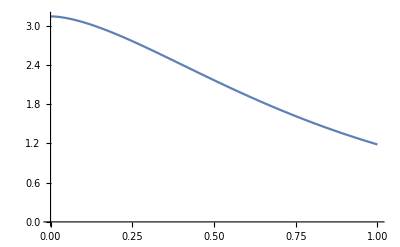

```mathematica
ListLinePlot[resultEavg]
```

InterpolatingFunction[{{0., 1.}}, <>]

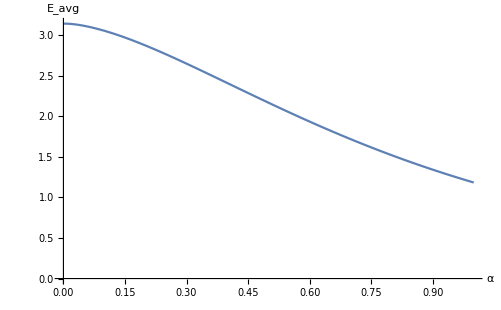

```mathematica
t=Table[resultEavg[[i]][[2]],{i,1,countY}];
fEavg=ListInterpolation[t,{0,1}]
Plot[fEavg[x],{x,0,1},PlotRange->{0,π}, AxesLabel->{"α","E_avg"}]
```

Export as binary float arays for C#:

```mathematica
t=Table[testResultEo[[i]][[3]],{i,1,countX*countY}];
Export["MSBRDF_E128x128.float",t,"Real32"]
t=Table[resultEavg[[i]][[2]],{i,1,countY}];
Export["MSBRDF_Eavg128.float",t,"Real32"]
```

MSBRDF_E128x128.float

MSBRDF_Eavg128.float

Fitting Eavg

{a→0.,b→-0.446898,c→-5.72019,d→6.61848,e→-2.41727}

π-0.446898 x-5.72019 x^2+6.61848 x^3-2.41727 x^4

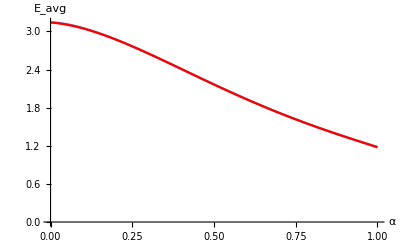

```mathematica
Clear[a,b,c,d,x]
fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";

modelEavg=π+0*a+(0+1*b)*x+c*x^2+d*x^3+e*x^4;
fitEavg=FindFit[resultEavg,modelEavg,{a,b,c,d,e},x,Method->fittingMethod]
modelEavg/.fitEavg
funcEavg=Function[x,Evaluate[modelEavg/.fitEavg]];
Show[
Plot[fEavg[x],{x,0,1},PlotRange->{0,π},AxesLabel->{"α","E_avg"}],
Plot[funcEavg[x],{x,0,1},PlotStyle->Red]
]
```

## Let’s check the BRDFs sum to π!

```mathematica
BRDFggx[θo_,θi_,ϕ_,α_]:= smith[θo,α]*smith[θi,α]*ggx[change[θo,θi,ϕi],α]
BRDFms[θo_,θi_,ϕ_,α_]:=((1-fEo[Cos[θo],α])*(1-fEo[Cos[θi],α]))/(π-fEavg[α])
```

```mathematica
whiteFurnace0[α_]:=2*π*NIntegrate[BRDFggx[θo,θi,ϕ,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
whiteFurnace1[α_]:=2*π*NIntegrate[BRDFms[θo,θi,ϕ,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
whiteFurnace[α_]:=2*π*NIntegrate[(BRDFggx[θo,θi,ϕ,α]+BRDFms[θo,θi,ϕ,α])*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
```

```mathematica
whiteFurnace0[0.3]
whiteFurnace1[0.3]
```

2.64771

0.493886

```mathematica
whiteFurnace[0.3]
```

3.14159

```mathematica
whiteFurnaceResult=Table[{α,whiteFurnace[Max[0.01,α]]},{α,0,1,0.1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.500047 and 0.000053884 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

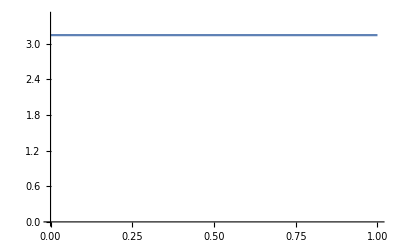

```mathematica
ListLinePlot[whiteFurnaceResult,PlotRange->{0,1.1*π}]
```

```mathematica
whiteFurnaceResult0=Table[{α,whiteFurnace0[Max[0.01,α]]},{α,0,1,0.05}]
whiteFurnaceResult1=Table[{α,whiteFurnace1[Max[0.01,α]]},{α,0,1,0.05}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.499733 and 0.0000510937 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.495579 and 1.18889×10^-6 for the integral and error estimates.

{{0.,3.13991},{0.05,3.11382},{0.1,3.05224},{0.15,2.96919},{0.2,2.87121},{0.25,2.76289},{0.3,2.64771},{0.35,2.52841},{0.4,2.4072},{0.45,2.28586},{0.5,2.16582},{0.55,2.0482},{0.6,1.93385},{0.65,1.82343},{0.7,1.7174},{0.75,1.61607},{0.8,1.51963},{0.85,1.42816},{0.9,1.34166},{0.95,1.26005},{1.,1.18323}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000314469 and 6.88027×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{{0.,0.00197587},{0.05,0.0277751},{0.1,0.0893483},{0.15,0.172407},{0.2,0.270382},{0.25,0.378701},{0.3,0.493886},{0.35,0.613187},{0.4,0.734392},{0.45,0.855729},{0.5,0.975771},{0.55,1.0934},{0.6,1.20774},{0.65,1.31816},{0.7,1.42419},{0.75,1.52552},{0.8,1.62196},{0.85,1.71343},{0.9,1.79993},{0.95,1.88154},{1.,1.95836}}

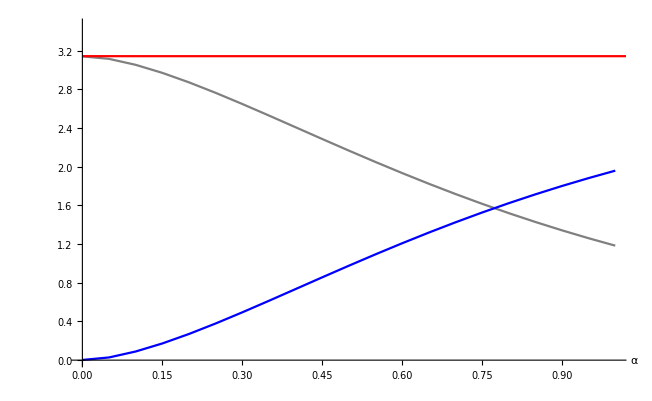

```mathematica
Show[
ListLinePlot[whiteFurnaceResult0,PlotRange->{0,1.1*π},PlotStyle->Gray,AxesLabel->{"α",""}],
ListLinePlot[whiteFurnaceResult1,PlotStyle->Blue],
ListLinePlot[whiteFurnaceResult0+whiteFurnaceResult1,PlotRange->Full,PlotStyle->Red]
]
```

### C# Simulation

```mathematica
(*SetDirectory[NotebookDirectory[]]; *)
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countX = 32;
countY= 32;
rawFile=BinaryReadList["MSBRDF_E"<>ToString[countX]<>"x"<>ToString[countY]<>".float", "Real32"];
simulEo=Table[{Mod[i,countX]/(countX-1),Quotient[i,countX]/(countY-1), rawFile[[1+i]]},{i,0,countX*countY-1}];
```

```mathematica
ListPlot3D[simulEo,PlotRange->{0,1},AxesLabel->{"cos(θ)","α"}]
```

-Graphics3D-

```mathematica
Image[Table[Table[1-simulEo[[1+countX*y+x]][[3]],{x,0,countX-1}],{y,0,countY-1}]]
```

-Graphics-

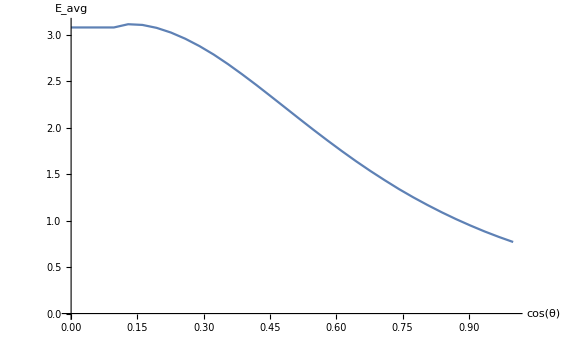

```mathematica
countX=32;
rawFileAvg=BinaryReadList["MSBRDF_Eavg32.float", "Real32"];
Eavg=Table[{Mod[i,countX]/(countX-1),rawFileAvg[[1+i]]},{i,0,countX-1}];
ListLinePlot[Eavg,AxesLabel->{"cos(θ)","E_avg"}]
```

### Importance Sampling of powers of cosine

```mathematica
Integrate[Cos[x]Sin[x],x]
```

-1/2 Cos[x]^2

```mathematica
D[Cos[x]^3,x]
```

-3 Cos[x]^2 Sin[x]

### Plotting Oren-Nayar Coefficients

Just to make sure the standard deviation σ is in radians! (they keep giving it in degrees, I started to be a bit skeptic for a moment)...

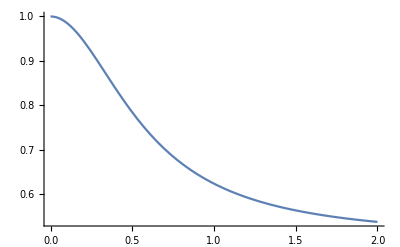

```mathematica
Plot[1-0.5 σ^2/(σ^2+0.33),{σ,0,2}]
```

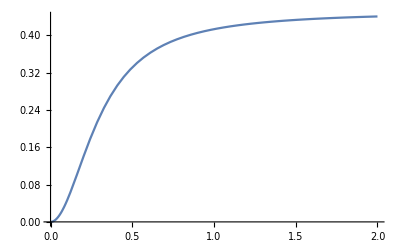

```mathematica
Plot[0.45 σ^2/(σ^2+0.09),{σ,0,2}]
```

# Oren-Nayar

```mathematica
oren=Function[ {θo,ϕo,θi,ϕi,α},
σ=π/2 α;
A = 1-0.5*σ^2/(σ^2+0.33);
B = 0.45*σ^2/(σ^2+0.09);
a=Max[θo,θi];
b=Min[θo,θi];
1/π(A+B*Max[0,Cos[ϕo-ϕi]]*Sin[a]*Tan[b])
];
oren[0,0,0.1,0.2,0.2]
```

0.281669

```mathematica
Manipulate[Plot3D[oren[θo,0,x,0,α],{x,0,π/2},{α,0,1},PlotRange->{0,1},AxesLabel->{"cos(θ)","α","Oren"}],{{θo,π/2},0,π/2}]
```

Let’s try integrating the Lambertian case:

```mathematica
α=0.0;
2*π*NIntegrate[oren[θo,0,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2}]
```

3.14159

```mathematica
orenEo[θo_,α_]:=NIntegrate[oren[θo,0,θi,ϕi,α] * Cos[θi]* Sin[θi],{θi,0,π/2},{ϕi,-π,π}]
orenEo[0.5,0.4]
```

0.769888

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countX = 32;
countY= 32;
tableFileName="MSBRDF_OrenNayar_E"  <>ToString[countX] <>"x" <> ToString[countY] <>".csv"
tableFileNameAvg="MSBRDF_OrenNayar_Eavg"  <>ToString[countY] <>".csv"

buildTable=Function[{i},
x=N[Mod[i,countX]/(countX-1)];
y=N[Quotient[i,countX]/(countY-1)];
θo=ArcCos[x];
α=y;
{x,y,Min[1,orenEo[θo,α]]}
]
buildTable[countX*5+7]
```

MSBRDF_OrenNayar_E32x32.csv

MSBRDF_OrenNayar_Eavg32.csv

Function[{i},x=N[Mod[i,countX]/(countX-1)];y=N[Quotient[i,countX]/(countY-1)];θo=ArcCos[x];α=y;{x,y,Min[1,orenEo[θo,α]]}]

{0.225806,0.16129,0.996768}

```mathematica
resultOrenEo= Table[buildTable[i],{i,0,countX*countY-1}];
Export[tableFileName,resultOrenEo,"CSV"]
```

MSBRDF_OrenNayar_E32x32.csv

```mathematica
Export[tableFileName,resultOrenEo,"CSV"]
```

```mathematica
ListPlot3D[resultOrenEo,PlotRange->{0,1},AxesLabel->{"cos(θ_o)","α"}]
Image[Table[Table[1-resultOrenEo[[1+countX*y+x]][[3]],{x,0,countX-1}],{y,0,countY-1}]]
```

-Graphics3D-

-Graphics-

Re-Importing and testing...

```mathematica
testResultOrenEo = Import[tableFileName,"CSV"];
ListPlot3D[testResultOrenEo,AxesLabel->{"cos(θ)", "α","E_i"}]
```

-Graphics3D-

Let’s reorder the table and create an interpolation function from it:

```mathematica
t=Table[testResultOrenEo[[1+countX*(y-1)+(x-1)]][[3]],{x,1,countY},{y,1,countY}];
fOrenEo=ListInterpolation[t,{{0,1},{0,1}}]
Plot3D[fOrenEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

-Graphics3D-

### Analytical fitting

```mathematica
Clear[a,b,c,d,e,f,x,y]
fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";

modelOrenEo=a+b*x+c*y+d*x^2+e*y^2+f*x^2*y+g*x*y^2+h*x^3+i*y^3+j*x^3*y+k*x*y^3+l*x^3*y^3;
modelOrenEo=(a+b*x+c*x^2+d*x^3) + (e+f*x+g*x^2+h*x^3)*y+ (i+j*x+k*x^2+l*x^3)*y^2+ (m+n*x+o*x^2+p*x^3)*y^3;
(*fitFuncOren[a_?NumericQ,b_?NumericQ,x_?NumericQ]:=y/.FindRoot[a y+b Log[y]==x,{y,1.}];*)
fitfunc[x_,y_,a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_]:=(a+b*x+c*x^2+d*x^3) + (e+f*x+g*x^2+h*x^3)*y+ (i+j*x+k*x^2+l*x^3)*y^2+ (m+n*x+o*x^2+p*x^3)*y^3
fitOrenEo=FindFit[resultOrenEo,fitfunc[x,y,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p],{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p},{x,y},Method->fittingMethod]
Show[
Plot3D[fOrenEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}],
Plot3D[Min[1,modelOrenEo/.fitOrenEo],{x,0,1},{y,0,1},PlotStyle->Red]
]
```

{a→1.0057,b→0.0458902,c→-0.0454034,d→0.0232934,e→0.056118,f→-0.771209,g→0.21819,h→-0.286582,i→-0.93392,j→0.838325,k→-0.0236121,l→0.227303,m→0.664248,n→-0.292948,o→-0.107221,p→-0.0352586}

-Graphics3D-

```mathematica
Clear[x,y,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q]
fitfunc[x_,y_,a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_,m_,n_,o_,p_]:=Min[1,(a+b*x+c*x^2+d*x^3) + (e+f*x+g*x^2+h*x^3)*y+ (i+j*x+k*x^2+l*x^3)*y^2+ (m+n*x+o*x^2+p*x^3)*y^3]
```

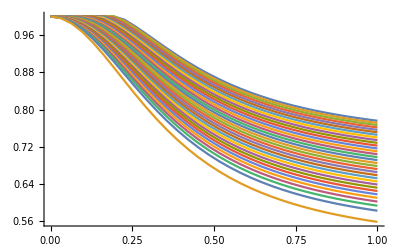

```mathematica
t=Table[{ (y-1)/(countX-1), testResultOrenEo[[1+countX*(y-1)+(x-1)]][[3]]},{x,1,countX},{y,1,countY}];
t[[1]];
ListLinePlot[t[[1]]];
Show[ListLinePlot[t]]
```

```mathematica
modelOrenEoY=a+b*y+c*y^2+d*y^3
fitsOrenEoY=Table[FindFit[t[[,modelOrenEoY,{a,b,c,d,e,f,g,h,i},{x,y},Method->fittingMethod]
Show[
Plot3D[fOrenEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}],
Plot3D[Min[1,modelOrenEo/.fitOrenEo],{x,0,1},{y,0,1},PlotStyle->Red]
]
```

### Computing Average Irradiance

Now let’s integrate the full white furnace irradiance using our table:

	E_avg(α)=∫E_o(θ_o,α) cos(θ_o) ⅆ θ_o

```mathematica
resultOrenEavg=Table[{N[i/(countY-1)],2*π*NIntegrate[fOrenEo[μ,i/(countY-1)]μ,{μ,0,1}]},{i,0,countY-1}]
Export[tableFileNameAvg,resultEavg,"CSV"]
```

{{0.,3.14159},{0.0322581,3.13724},{0.0645161,3.12342},{0.0967742,3.09846},{0.129032,3.06099},{0.16129,3.01112},{0.193548,2.95093},{0.225806,2.88414},{0.258065,2.81461},{0.290323,2.74519},{0.322581,2.67792},{0.354839,2.61412},{0.387097,2.55455},{0.419355,2.49955},{0.451613,2.44916},{0.483871,2.40324},{0.516129,2.36154},{0.548387,2.32375},{0.580645,2.28953},{0.612903,2.25857},{0.645161,2.23053},{0.677419,2.20513},{0.709677,2.18209},{0.741935,2.16116},{0.774194,2.14212},{0.806452,2.12477},{0.83871,2.10894},{0.870968,2.09446},{0.903226,2.0812},{0.935484,2.06903},{0.967742,2.05785},{1.,2.04755}}

MSBRDF_OrenNayar_Eavg32.csv

```mathematica
Export[tableFileNameAvg,resultEavg,"CSV"]
```

MSBRDF_OrenNayar_Eavg32.csv

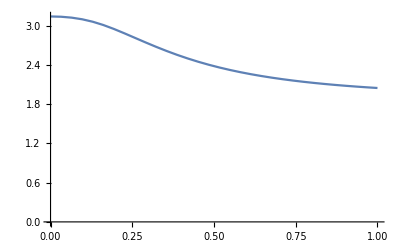

```mathematica
ListLinePlot[resultOrenEavg,PlotRange->{0,π}]
```

InterpolatingFunction[{{0., 1.}}, <>]

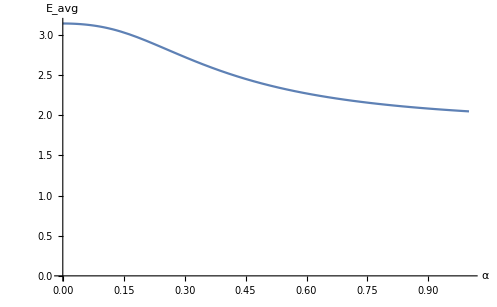

```mathematica
t=Table[resultOrenEavg[[i]][[2]],{i,1,countY}];
fOrenEavg=ListInterpolation[t,{0,1}]
Plot[fOrenEavg[x],{x,0,1},PlotRange->{0,π}, AxesLabel->{"α","E_avg"}]
```

{a→0.,b→0.,c→-7.49231,d→11.4409,e→-5.05903}

π-7.49231 x^2+11.4409 x^3-5.05903 x^4

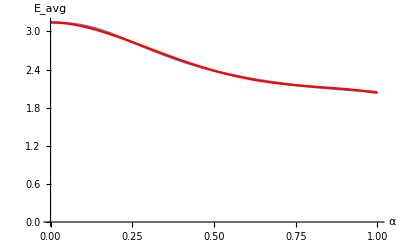

```mathematica
Clear[a,b,c,d,x]
fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";

modelOrenEavg=π+0*a+(0+0*b)*x+c*x^2+d*x^3+e*x^4;
fitOrenEavg=FindFit[resultOrenEavg,modelOrenEavg,{a,b,c,d,e},x,Method->fittingMethod]
modelOrenEavg/.fitOrenEavg
funcOrenEavg=Function[x,Evaluate[modelOrenEavg/.fitOrenEavg]];
Show[
Plot[fOrenEavg[x],{x,0,1},PlotRange->{0,π},AxesLabel->{"α","E_avg"}],
Plot[funcOrenEavg[x],{x,0,1},PlotStyle->Red]
]
```

## Let’s check the BRDFs sum to π!

```mathematica
BRDForen[θo_,θi_,ϕ_,α_]:= oren[θo,0,θi,ϕ,α]
BRDForenms[θo_,θi_,ϕ_,α_]:=((1-fOrenEo[Cos[θo],α])*(1-fOrenEo[Cos[θi],α]))/(π-fOrenEavg[α])
```

```mathematica
whiteFurnace0[α_]:=2*π*NIntegrate[BRDForen[θo,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
whiteFurnace1[α_]:=2*π*NIntegrate[BRDForenms[θo,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
whiteFurnace[α_]:=2*π*NIntegrate[(BRDForen[θo,θi,ϕi,α]+BRDForenms[θo,θi,ϕi,α])*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
```

```mathematica
whiteFurnace0[0.3]
whiteFurnace1[0.3]
```

2.72499

0.416867

```mathematica
whiteFurnace[0.3]
```

3.14213

```mathematica
whiteFurnaceResult0=Table[{α,whiteFurnace0[α]},{α,0,1,0.05}]
whiteFurnaceResult1=Table[{α,whiteFurnace1[α]},{α,0,1,0.05}]
```

{{0.,3.14159},{0.05,3.13217},{0.1,3.0974},{0.15,3.03079},{0.2,2.93817},{0.25,2.83233},{0.3,2.72499},{0.35,2.62373},{0.4,2.53232},{0.45,2.4519},{0.5,2.38222},{0.55,2.3223},{0.6,2.27094},{0.65,2.22692},{0.7,2.18913},{0.75,2.15659},{0.8,2.12848},{0.85,2.10409},{0.9,2.08285},{0.95,2.06426},{1.,2.04793}}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{0.,0.},{0.05,0.0106767},{0.1,0.0463195},{0.15,0.111741},{0.2,0.203616},{0.25,0.309496},{0.3,0.416867},{0.35,0.518153},{0.4,0.60959},{0.45,0.690019},{0.5,0.759711},{0.55,0.819639},{0.6,0.871008},{0.65,0.915032},{0.7,0.952826},{0.75,0.985365},{0.8,1.01348},{0.85,1.03787},{0.9,1.05912},{0.95,1.07771},{1.,1.09404}}

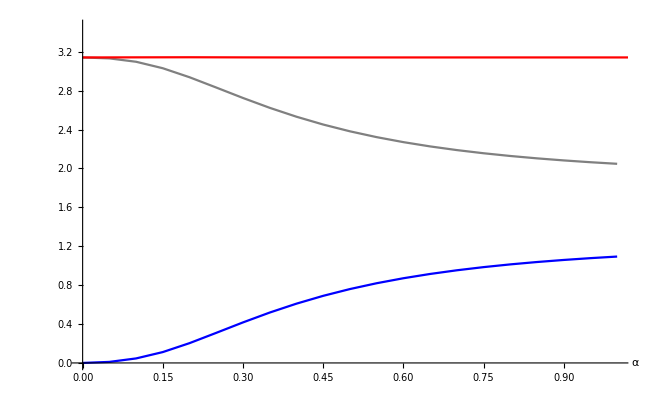

```mathematica
Show[
ListLinePlot[whiteFurnaceResult0,PlotRange->{0,1.1*π},PlotStyle->Gray,AxesLabel->{"α",""}],
ListLinePlot[whiteFurnaceResult1,PlotStyle->Blue],
ListLinePlot[whiteFurnaceResult0+whiteFurnaceResult1,PlotRange->Full,PlotStyle->Red]
]
```

### Fresnel

```mathematica
fresnel=Function[{c,F0},
η=(1+√F0)/(1.0000001-√F0);
g=√(η^2-1+c^2);
1/2((g-c)/(g+c))^2(1+((c*(g+c)-1)/(c*(g-c)+1))^2)
];
F0=1.0;
Manipulate[Plot[fresnel[Cos[θ],F0],{θ,0,π/2},PlotRange->{0,1.1}],{{F0,1},0,1}]
```

```mathematica
fresnelH=Function[{θo,θi,F0},
lengthH=√(2+2*Cos[θo-θi]);
cosH=(Cos[θo]+Cos[θi])/lengthH;
fresnel[cosH,F0]
];
Manipulate[Plot[fresnelH[θo,θi,F0],{θi,-π/2,π/2},PlotRange->{0,1}],{{θo,0},-π/2,π/2},{{F0,1},0,1}]
Manipulate[Plot[fresnel[Cos[θo],F0]*fresnel[Cos[θi],F0],{θi,-π/2,π/2},PlotRange->{0,1}],{{θo,0},-π/2,π/2},{{F0,1},0,1}]
```

```mathematica
Manipulate[
Show[
Plot[fresnelH[θo,θi,F0],{θi,-π/2,π/2},PlotRange->{0,1}],
Plot[fresnel[Cos[θo],F0]*fresnel[Cos[θi],F0],{θi,-π/2,π/2},PlotRange->{0,1},PlotStyle->Red]
]
,{{θo,0},-π/2,π/2},{{F0,1},0,1}]
```

# Simulated Multiple-Scattering Fresnel Factor

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countTheta = 20;
countRoughness= 10;
countF0=20;
countOrders=7;
taRawTotalReflectances=Table[
Import["TotalReflectance_"  <>ToString[countTheta] <>"x"  <>ToString[countRoughness] <>"x"  <>ToString[countF0] <>"_order"  <>ToString[order] <>".bin", "Real64"],{order,1,countOrders}];
```

```mathematica
Table[{N[Mod[i-1,countTheta]/countTheta*π/2],N[1-Quotient[i-1,countTheta]/(countRoughness-1)],taRawTotalReflectances[[1]][[i]]},{i,1,countTheta*countRoughness}];
Length[taRawTotalReflectances[[1]]]
```

4000

```mathematica
taTotalReflectances=Table[
Table[
Table[{N[Mod[i-1,countTheta]/countTheta*π/2],N[1-Quotient[i-1,countTheta]/(countRoughness-1)],taRawTotalReflectances[[order]][[k*countTheta*countRoughness+ i]]},{i,1,countTheta*countRoughness}]
,{k,0,countF0-1}]
,{order,1,countOrders}];
```

```mathematica
taTotalReflectances[[1]][[1]];
```

```mathematica
Manipulate[
ListPlot3D[taTotalReflectances[[order]][[F0]],PlotRange->{0,0.2},AxesLabel->{"θ","α"}],{{order,2},1,countOrders,1},{F0,1,countF0,1}
]
```

## Show Total Reflectance Depending on F_0

```mathematica
taSum=Table[
Table[{N[Mod[i-1,countTheta]/countTheta*π/2],N[1-Quotient[i-1,countTheta]/(countRoughness-1)],
Sum[taRawTotalReflectances[[order]][[k*countTheta*countRoughness+ i]],{order,1,countOrders}]
},{i,1,countTheta*countRoughness}]
,{k,0,countF0-1}];
Manipulate[ListPlot3D[taSum[[F0]],PlotRange->{0,1},AxesLabel->{"θ","α"}],{F0,1,countF0,1}]
```

```mathematica
taSum2=Table[
Table[{N[Mod[i-1,countTheta]/countTheta*π/2],N[1-Quotient[i-1,countTheta]/(countRoughness-1)],
Sum[taRawTotalReflectances[[order]][[k*countTheta*countRoughness+ i]],{order,2,countOrders}]
},{i,1,countTheta*countRoughness}]
,{k,0,countF0-1}];
Manipulate[ListPlot3D[taSum2[[F0]],PlotRange->{0,0.4},AxesLabel->{"θ","α"}],{F0,1,countF0,1}]
```